```mathematica
N[Solve[(k1 c2 -1/te-1/ti-k2 c6)/(2 k1 c2)==(-c10-Sqrt[c10 ^2-4 c9 c11])/(2 c9)]]
```

{{Jee→0.0345459-2.01228×10^-16 ⅈ},{Jee→0.62309+7.21645×10^-16 ⅈ}}

```mathematica
(*ce for excitatory gain, ci for inhibitory gain. eIth and iIth the different thresholds *)
ti=2 ; te= 100;   ce = 310 (*gain factor*); ci= 615; Io= 1/10 (*background*); eIth= 125;iIth= 177; Is=1/20(*stimulus*);a=64/100; (*linear estimate for excitaory and inhibitory input-output functions*) k1 = 310/1000;k2=615/1000 ;(*1/1000 for unit consistency*);
```

```mathematica
Io=.2;Jie=.08;Jii=.02; Jee=0.79235226801625;
```

```mathematica
Clear[Si,Se]
```

```mathematica
Si=k2(c4+c2 Se)/(1/ti + k2 c6);
```

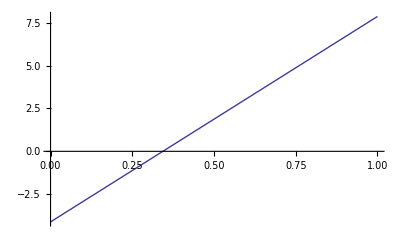

```mathematica
p1=Plot[Si,{Se,0,1}]
```

```mathematica
Clear[Si,Se]
```

```mathematica
Si2=1/c3(c1+c2 Se-Se/(te  k1(1-Se)))
```

0.063004 (-30.4+157.203 Se-Se/(31 (1-Se)))

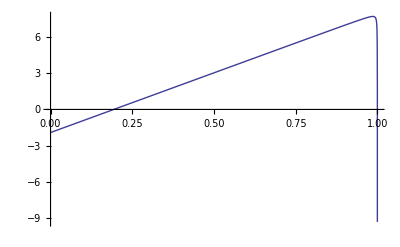

```mathematica
p2=Plot[Si2,{Se,0,1}]
```

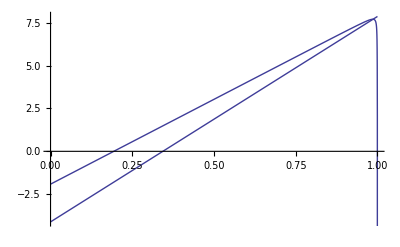

```mathematica
Show[p1,p2]
```

```mathematica
Clear[c7]
```

```mathematica
c10
```

5.2662